```mathematica
Integrate[x/(x^2+1),x]
```

1/2 Log[1+x^2]

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Integrate[x^4/(x^2+1),x]
```

-x+x^3/3+ArcTan[x]

```mathematica
Integrate[1/(1+y^2/a^2)^(3/2),{y,-a,a}]
```

√2 a

```mathematica
Integrate[(x/a)^m,{x,-a,a}]
```

ConditionalExpression[((1+(-1)^m) a)/(1+m),a∈ℝ&&Re[m]>-1]

```mathematica
DSolve[f''[r]+1/r f'[r]==λ/(2π ϵ0 r) DiracDelta[r],f[r],r]
```

$Aborted

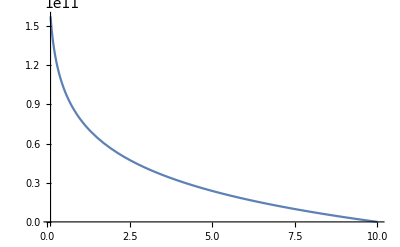

```mathematica
Block[
{λ=-1.9,f,r,ϵ0=8.85*10^(-12),potent,R=10},
potent=NDSolveValue[{f''[r]+1/r f'[r]==-λ/(2π ϵ0 r) DiracDelta[r],f[R]==0,f'[R]==λ/(2π ϵ0 R)},f[r],{r,0.01R,R}];
Plot[potent/.{r->r1},{r1,0.01R,R}]
]
```

```mathematica
Block[
{λ=-1.9,f,r,ϵ0=8.85*10^(-12),potent,R=10^(-12),θ},
potent=NDSolveValue[{D[f[r,θ],{r,2}]+1/r D[f[r,θ],r]+1/r^2D[f[r,θ],{θ,2}]==-λ/(2π ϵ0 r)DiracDelta[r],f[R,θ]==0},f[r,θ],{r,0,R},{θ,0,2π}];
ContourPlot[(potent)/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]},{x,-R,R},{y,-R,R}]
]
```

$Aborted

```mathematica
Integrate[(x/a)^(2m),{x,-a,a}]
```

ConditionalExpression[((1+(-1)^(2 m)) a)/(1+2 m),a∈ℝ&&Re[m]>-1/2]

```mathematica
Integrate[(x-z)/((x-z)^2+y^2)(z/a)^(2m),z]
```

((z/a)^(2 m) (-(z/(-x+ⅈ y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x-ⅈ y)/(x-ⅈ y-z)]-(z/(-x-ⅈ y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x+ⅈ y)/(x+ⅈ y-z)]))/(4 m)

```mathematica
Limit[((z/a)^(2 m) (-(z/(-x+ⅈ y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x-ⅈ y)/(x-ⅈ y-z)]-(z/(-x-ⅈ y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x+ⅈ y)/(x+ⅈ y-z)]))/(4 m),z->-a,Assumptions->m∈Integers]
```

-(a^(-4 m) (a^2+2 a x+x^2+y^2)^(2 m) ((a/(a+x+ⅈ y))^(2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x-ⅈ y)/(a+x-ⅈ y)]+(a/(a+x-ⅈ y))^(2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x+ⅈ y)/(a+x+ⅈ y)]))/(4 m)

```mathematica
FullSimplify[(x-z)/((x-z)^2+y^2)+x/(x^2+(y-z)^2)]
```

x/(x^2+(y-z)^2)+(x-z)/(y^2+(x-z)^2)

```mathematica
Integrate[x/(x^2+(y-z)^2)(z/a)^(2m),z]
```

(ⅈ (z/a)^(2 m) ((z/(ⅈ x-y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x+ⅈ y)/(x+ⅈ (y-z))]-(z/(-ⅈ x-y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(ⅈ x+y)/(ⅈ x+y-z)]))/(4 m)

```mathematica
Limit[(ⅈ (z/a)^(2 m) ((z/(ⅈ x-y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x+ⅈ y)/(x+ⅈ (y-z))]-(z/(-ⅈ x-y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(ⅈ x+y)/(ⅈ x+y-z)]))/(4 m),z->-a,Assumptions->m∈Integers]
```

(ⅈ a^(-4 m) (a^2+x^2+2 a y+y^2)^(2 m) ((a/(a+ⅈ x+y))^(2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(-ⅈ x+y)/(a-ⅈ x+y)]-(a/(a-ⅈ x+y))^(2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(ⅈ x+y)/(a+ⅈ x+y)]))/(4 m)

```mathematica
Limit[(ⅈ (z/a)^(2 m) ((z/(ⅈ x-y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(x+ⅈ y)/(x+ⅈ (y-z))]-(z/(-ⅈ x-y+z))^(-2 m) Hypergeometric2F1[-2 m,-2 m,1-2 m,(ⅈ x+y)/(ⅈ x+y-z)]))/(4 m),z->a,Assumptions->m∈Integers]
```

Indeterminate

```mathematica
Integrate[x/((y-z)^2+x^2)+(x-z)/((x-z)^2+y^2),z]
```

-ArcTan[(y-z)/x]-1/2 Log[y^2+(x-z)^2]

```mathematica
Limit[-ArcTan[(y-z)/x]-1/2 Log[y^2+(x-z)^2],z->-a]
```

-ArcTan[(a+y)/x]-1/2 Log[(a+x)^2+y^2]

```mathematica
Limit[-ArcTan[(y-z)/x]-1/2 Log[y^2+(x-z)^2],z->a]
```

ArcTan[(a-y)/x]-1/2 Log[(a-x)^2+y^2]

```mathematica
FullSimplify[(ArcTan[(a-y)/x]-1/2 Log[(a-x)^2+y^2])-(-ArcTan[(a+y)/x]-1/2 Log[(a+x)^2+y^2])]
```

ArcTan[(a-y)/x]+ArcTan[(a+y)/x]-1/2 Log[(a-x)^2+y^2]+1/2 Log[(a+x)^2+y^2]

```mathematica
Integrate[(y-z)/((y-z)^2+x^2)+y/((x-z)^2+y^2),z]
```

-ArcTan[(x-z)/y]-1/2 Log[x^2+(y-z)^2]

```mathematica
Limit[-ArcTan[(x-z)/y]-1/2 Log[x^2+(y-z)^2],z->-a]
```

-ArcTan[(a+x)/y]-1/2 Log[x^2+(a+y)^2]

```mathematica
Limit[-ArcTan[(x-z)/y]-1/2 Log[x^2+(y-z)^2],z->a]
```

ArcTan[(a-x)/y]-1/2 Log[x^2+(a-y)^2]

```mathematica
FullSimplify[(ArcTan[(a-x)/y]-1/2 Log[x^2+(a-y)^2])-(-ArcTan[(a+x)/y]-1/2 Log[x^2+(a+y)^2])]
```

ArcTan[(a-x)/y]+ArcTan[(a+x)/y]-1/2 Log[x^2+(a-y)^2]+1/2 Log[x^2+(a+y)^2]

```mathematica
Integrate[((x+a)/((x+a)^2+(y-z)^2)+(x-z)/((x-z)^2+(y+a)^2)),z]
```

-ArcTan[(y-z)/(a+x)]-1/2 Log[a^2+2 a y+y^2+(x-z)^2]

```mathematica
Limit[-ArcTan[(y-z)/(a+x)]-1/2 Log[a^2+2 a y+y^2+(x-z)^2],z->a]
```

ArcTan[(a-y)/(a+x)]-1/2 Log[a^2+(a-x)^2+2 a y+y^2]

```mathematica
Limit[-ArcTan[(y-z)/(a+x)]-1/2 Log[a^2+2 a y+y^2+(x-z)^2],z->-a]
```

-ArcTan[(a+y)/(a+x)]-1/2 Log[a^2+(a+x)^2+2 a y+y^2]

```mathematica
FullSimplify[(ArcTan[(a-y)/(a+x)]-1/2 Log[a^2+(a-x)^2+2 a y+y^2])-(-ArcTan[(a+y)/(a+x)]-1/2 Log[a^2+(a+x)^2+2 a y+y^2])]
```

ArcTan[(a-y)/(a+x)]+ArcTan[(a+y)/(a+x)]-1/2 Log[a^2+(a-x)^2+2 a y+y^2]+1/2 Log[a^2+(a+x)^2+2 a y+y^2]

```mathematica
Limit[ArcTan[(a-y)/(a+x)]+ArcTan[(a+y)/(a+x)]-1/2 Log[a^2+(a-x)^2+2 a y+y^2]+1/2 Log[a^2+(a+x)^2+2 a y+y^2],{x->-a,y->-a}]
```

-∞

```mathematica
Integrate[((y +a)/((y+a)^2+(x-z)^2)+(y-z)/((y-z)^2+(x+a)^2)),z]
```

-ArcTan[(x-z)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(y-z)^2]

```mathematica
Limit[-ArcTan[(x-z)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(y-z)^2],z->-a]
```

-ArcTan[(a+x)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(a+y)^2]

```mathematica
Limit[-ArcTan[(x-z)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(y-z)^2],z->a]
```

ArcTan[(a-x)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(a-y)^2]

```mathematica
FullSimplify[(ArcTan[(a-x)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(a-y)^2])-(-ArcTan[(a+x)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(a+y)^2])]
```

ArcTan[(a-x)/(a+y)]+ArcTan[(a+x)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(a-y)^2]+1/2 Log[a^2+2 a x+x^2+(a+y)^2]

```mathematica
Limit[ArcTan[(a-x)/(a+y)]+ArcTan[(a+x)/(a+y)]-1/2 Log[a^2+2 a x+x^2+(a-y)^2]+1/2 Log[a^2+2 a x+x^2+(a+y)^2],{x->-a,y->-a}]
```

Indeterminate

```mathematica
Integrate[((x+a)/((x+a)^2+(y-z)^2)+(x-z)/((x-z)^2+(y+a)^2))(z/a)^2,z]
```

1/(2 a^2)(-2 a x+x^2+2 a z-z^2+4 x (a+y) ArcTan[(a+y)/(x-z)]-2 (a^2+2 a x+x^2-y^2) ArcTan[(a+x)/(y-z)]+2 a y Log[a^2+2 a x+x^2+(y-z)^2]+2 x y Log[a^2+2 a x+x^2+(y-z)^2]+a^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2]-x^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2]+2 a y Log[a^2+x^2+2 a y+y^2-2 x z+z^2]+y^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2])

```mathematica
Limit[1/(2 a^2)(-2 a x+x^2+2 a z-z^2+4 x (a+y) ArcTan[(a+y)/(x-z)]-2 (a^2+2 a x+x^2-y^2) ArcTan[(a+x)/(y-z)]+2 a y Log[a^2+2 a x+x^2+(y-z)^2]+2 x y Log[a^2+2 a x+x^2+(y-z)^2]+a^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2]-x^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2]+2 a y Log[a^2+x^2+2 a y+y^2-2 x z+z^2]+y^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2]),z->-a]
```

1/(2 a^2)(-3 a^2-2 a x+x^2-2 (a^2+2 a x+x^2-y^2) ArcTan[(a+x)/(a+y)]+4 x (a+y) ArcTan[(a+y)/(a+x)]+2 a y Log[a^2+2 a x+x^2+(a+y)^2]+2 x y Log[a^2+2 a x+x^2+(a+y)^2]+a^2 Log[2 a^2+x^2+y^2+2 a (x+y)]-x^2 Log[2 a^2+x^2+y^2+2 a (x+y)]+2 a y Log[2 a^2+x^2+y^2+2 a (x+y)]+y^2 Log[2 a^2+x^2+y^2+2 a (x+y)])

```mathematica
Series[1/(2 a^2)(-2 a x+x^2+2 a z-z^2+4 x (a+y) ArcTan[(a+y)/(x-z)]-2 (a^2+2 a x+x^2-y^2) ArcTan[(a+x)/(y-z)]+2 a y Log[a^2+2 a x+x^2+(y-z)^2]+2 x y Log[a^2+2 a x+x^2+(y-z)^2]+a^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2]-x^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2]+2 a y Log[a^2+x^2+2 a y+y^2-2 x z+z^2]+y^2 Log[a^2+x^2+2 a y+y^2-2 x z+z^2]),{z,a,1}]
```

1/(2 a^2)(a^2-2 a x+x^2-2 (a^2+2 a x+x^2-y^2) ArcTan[(a+x)/(-a+y)]+4 x (a+y) ArcTan[(a+y)/(-a+x)]+2 a y Log[2 a^2+2 a x+x^2-2 a y+y^2]+2 x y Log[2 a^2+2 a x+x^2-2 a y+y^2]+a^2 Log[2 a^2-2 a x+x^2+2 a y+y^2]-x^2 Log[2 a^2-2 a x+x^2+2 a y+y^2]+2 a y Log[2 a^2-2 a x+x^2+2 a y+y^2]+y^2 Log[2 a^2-2 a x+x^2+2 a y+y^2])+(2 (x^3+2 a^2 y+x y^2) (z-a))/((2 a^2+2 a x+x^2-2 a y+y^2) (2 a^2-2 a x+x^2+2 a y+y^2))+O[z-a]^2

```mathematica
Limit[1/(2 a^2)(a^2-2 a x+x^2-2 (a^2+2 a x+x^2-y^2) ArcTan[(a+x)/(-a+y)]+4 x (a+y) ArcTan[(a+y)/(-a+x)]+2 a y Log[2 a^2+2 a x+x^2-2 a y+y^2]+2 x y Log[2 a^2+2 a x+x^2-2 a y+y^2]+a^2 Log[2 a^2-2 a x+x^2+2 a y+y^2]-x^2 Log[2 a^2-2 a x+x^2+2 a y+y^2]+2 a y Log[2 a^2-2 a x+x^2+2 a y+y^2]+y^2 Log[2 a^2-2 a x+x^2+2 a y+y^2]),{x->-a,y->-a}]
```

2-1/2 Log[4 a^2]

```mathematica
Limit[1/(2 a^2)(-3 a^2-2 a x+x^2-2 (a^2+2 a x+x^2-y^2) ArcTan[(a+x)/(a+y)]+4 x (a+y) ArcTan[(a+y)/(a+x)]+2 a y Log[a^2+2 a x+x^2+(a+y)^2]+2 x y Log[a^2+2 a x+x^2+(a+y)^2]+a^2 Log[2 a^2+x^2+y^2+2 a (x+y)]-x^2 Log[2 a^2+x^2+y^2+2 a (x+y)]+2 a y Log[2 a^2+x^2+y^2+2 a (x+y)]+y^2 Log[2 a^2+x^2+y^2+2 a (x+y)]),{x->-a,y->-a}]
```

Indeterminate

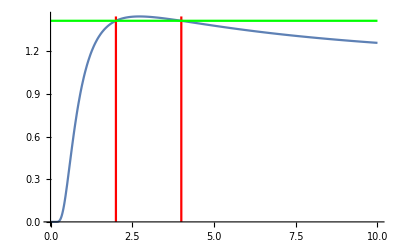

```mathematica
Show[
Plot[x^(1/x),{x,0,10},AxesOrigin->{0,0}],
ParametricPlot[{2,x},{x,0,E^(1/E)},PlotStyle->Red],
ParametricPlot[{4,x},{x,0,E^(1/E)},PlotStyle->Red],
ParametricPlot[{x,Sqrt[2]},{x,0,10},PlotStyle->Green]
]
```

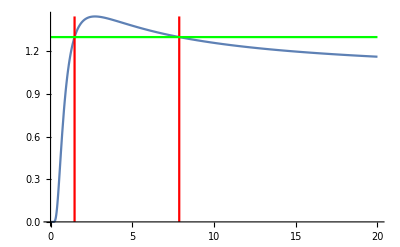

```mathematica
With[
{N1=20},
Show[
Plot[x^(1/x),{x,0,N1},AxesOrigin->{0,0}],
ParametricPlot[{7.8734,x},{x,0,E^(1/E)},PlotStyle->Red],
ParametricPlot[{1.47,x},{x,0,E^(1/E)},PlotStyle->Red],
ParametricPlot[{x,1.47^(1/1.47)},{x,0,N1},PlotStyle->Green]
]]
```

```mathematica
FindRoot[1.47^(1/1.47)==x^(1/x),{x,6.5}]
```

{x→7.87343}

```mathematica
1.47^(1/1.47)
```

1.29963

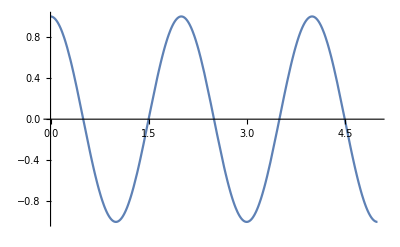

```mathematica
Plot[Cos[x π],{x,0,5}]
```